```mathematica
g[r_,m_]:=Exp[-1.3(r-m)^2]
```

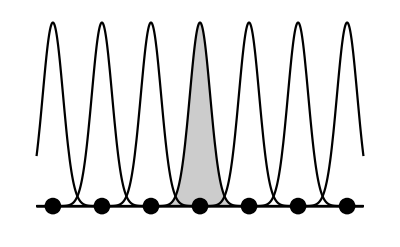

```mathematica
g1=Show[Plot[{g[r,0],g[r,3],g[r,-3],g[r,-6],g[r,6],g[r,-9],g[r,9]},{r,-10,10},PlotRange->{-.1,1},PlotStyle->Black,Axes->False,Filling->{1->Axis}],Graphics[{PointSize[0.03],Point[{{0,0},{-3,0},{3,0},{-6,0},{6,0},{-9,0},{9,0}}]}]]
```

```mathematica
gauss[i_,r_,m_]:=norm[[i]]Exp[-expo[[i]](r-m)^2];
expo={2,1};
norm={1,0.5};
```

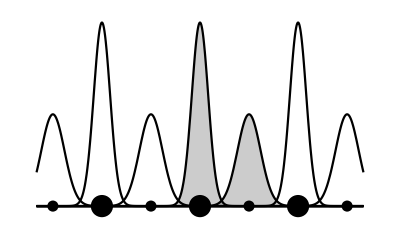

```mathematica
g1=Show[Plot[{gauss[1,r,0],gauss[2,r,3],gauss[1,r,6],gauss[2,r,9],gauss[1,r,-6],gauss[2,r,-3],gauss[2,r,-9]},{r,-10,10},PlotRange->{-.1,1},PlotStyle->Black,Axes->False,Filling->{1->Axis,2->Axis}],Graphics[{PointSize[0.04],Point[{{0,0},{6,0},{-6,0}}],PointSize[0.02],Point[{{3,0},{9,0},{-3,0},{-9,0}}]}]]
```

```mathematica
Export["Figura_dos_gaussianas_1D.png",g1]
```

Figura_dos_gaussianas_1D.png

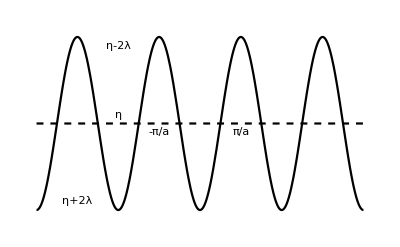

```mathematica
η=-2;
λ=-1.5;
a=2;
g1=Show[Plot[{η,η+2λ Cos[k*a]},{k,-2Pi,2Pi},Axes->False,PlotStyle->{{Black,Dashed},{Black,Line}},GridLines->{{-Pi/a,Pi/a},{η+2λ,η-2λ}},PlotRange->{Automatic,{η+2λ-.5,η-2λ+.5}}],Graphics[{Text["η-2λ",{-2Pi/a,η-2λ-.3}],Text["η+2λ",{-3Pi/a,η+2λ+.3}],Text["η",{-2Pi/a,η+.3}],Text["-π/a",{-Pi/a,η-.3}],Text["π/a",{Pi/a,η-.3}]}]]
```

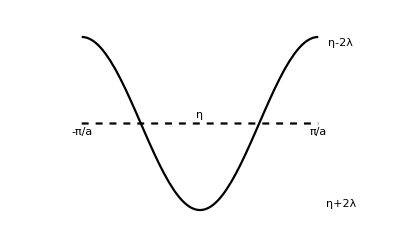

```mathematica
g1=Show[Plot[{η,η+2λ Cos[k*a]},{k,-Pi/a,Pi/a},Axes->False,PlotStyle->{{Black,Dashed},{Black,Line}},GridLines->{{-Pi/a,Pi/a},{η+2λ,η-2λ}},PlotRange->{{-Pi/a-0.6,Pi/a+0.6},{η+2λ-.5,η-2λ+.5}}],Graphics[{Text["η-2λ",{Pi/a+.3,η-2λ-.2}],Text["η+2λ",{Pi/a+0.3,η+2λ+.2}],Text["η",{0,η+.3}],Text["-π/a",{-Pi/a,η-.3}],Text["π/a",{Pi/a,η-.3}]}]]
```

```mathematica
Export["Figura_TB_1D_2.png",g1]
```

Figura_TB_1D_2.png

```mathematica
?Text
```

Text[expr] displays with expr in plain text format. 
Text[expr,coords] is a graphics primitive that displays the textual form of expr centered at the point specified by coords.

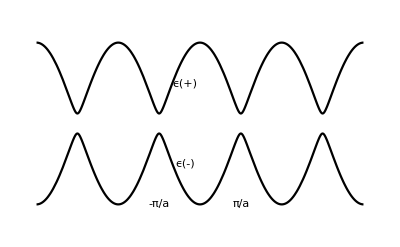

```mathematica
η1=-2;
η2=-1.5;
λ1=-1.;
a=2;
raiz[η1_,η2_,λ1_,k_]:=(1/2)Sqrt[(η1-η2)^2-8λ1(1+Cos[k*a])];
primer[η1_,η2_]:=(1/2)(η1+η2);
emas[η1_,η2_,λ1_,k_]=primer[η1,η2]+raiz[η1,η2,λ1,k];
emenos[η1_,η2_,λ1_,k_]=primer[η1,η2]-raiz[η1,η2,λ1,k];
g1=Show[Plot[{emenos[η1,η2,λ1,k],emas[η1,η2,λ1,k]},{k,-2Pi,2Pi},Axes->False,PlotStyle->{{Black,Black},{Black,Line}},GridLines->{{-Pi/a,Pi/a},None},PlotRange->{Automatic,{emenos[η1,η2,λ1,0]-.5,emas[η1,η2,λ1,0]+.5}}],Graphics[{Text["ϵ(-)",{-Pi/a+1,emenos[η1,η2,λ1,-Pi/a+.5]}],Text["ϵ(+)",{-Pi/a+1,emas[η1,η2,λ1,-Pi/a+0.5]}],Text["-π/a",{-Pi/a,emenos[η1,η2,λ1,0]}],Text["π/a",{Pi/a,emenos[η1,η2,λ1,0]}]}]]
```

```mathematica
Export["Figura_TB_1D_dos_atomos_1.png",g1]
```

Figura_TB_1D_dos_atomos_1.png

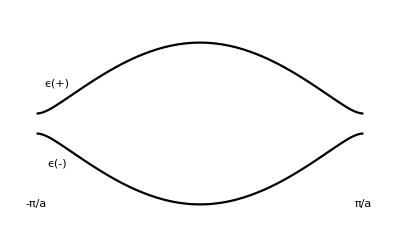

```mathematica
g1=Show[Plot[{emenos[η1,η2,λ1,k],emas[η1,η2,λ1,k]},{k,-Pi/a,Pi/a},Axes->False,PlotStyle->{{Black,Black},{Black,Line}},GridLines->{{-Pi/a,Pi/a},None},PlotRange->{Automatic,{emenos[η1,η2,λ1,0]-.5,emas[η1,η2,λ1,0]+.5}}],Graphics[{Text["ϵ(-)",{-Pi/a+.2,emenos[η1,η2,λ1,-Pi/a+.5]}],Text["ϵ(+)",{-Pi/a+.2,emas[η1,η2,λ1,-Pi/a+0.5]}],Text["-π/a",{-Pi/a,emenos[η1,η2,λ1,0]}],Text["π/a",{Pi/a,emenos[η1,η2,λ1,0]}]}]]
```

```mathematica
Export["Figura_TB_1D_dos_atomos_2.png",g1]
```

Figura_TB_1D_dos_atomos_2.png